```mathematica
HermN[n_,x_]:=(2^n n! √π)^(-1/2)ⅇ^(-x^2/2)HermiteH[n,x]
```

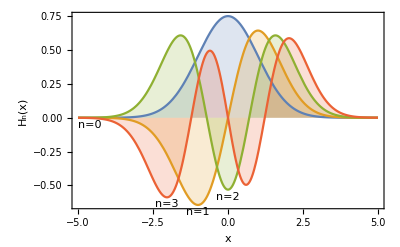

```mathematica
Plot[{HermN[0,x],HermN[1,x],HermN[2,x],HermN[3,x]},{x,-5,5},PlotRange->All,Frame->True,AxesLabel->{"x","H_n(x)"},BaseStyle->{FontSize->14},Filling->Axis,PlotLabels->Placed[{"n=0","n=1","n=2","n=3"},Below]]
```